```mathematica
r[n_]:=Module[{a,b},a={};For[i=1,i≤n,i++,b=RandomInteger[{1,9}];While[MemberQ[a,b],b=RandomInteger[{1,9}]];AppendTo[a,b]];a]
```

```mathematica
dtn[L_]:=Fold[10#1+#2&,0,L]
```

```mathematica
col["A"]=RGBColor[1,0,0];
col["B"]=RGBColor[0,1,0];
col["C"]=RGBColor[0,0,1];
col["D"]=RGBColor[1,.9,0];
col["E"]=RGBColor[.8,0,1];
```

```mathematica
gr[L_,s1_,s_,s2_]:=Module[{},Print[Show[Graphics[{AbsoluteThickness[4],Text[Style["+",FontSize->28],{0,1}],If[Length[s]==4,Line[{{0.5,0.4},{4.5,0.4}}],Line[{{-0.5,0.4},{4.5,0.4}}]],Table[{col[s1⟦ii,jj⟧],Line[{{jj-0.4,ii-0.4},{jj+0.4,ii-0.4},{jj+0.4,ii+0.4},{jj-0.4,ii+0.4},{jj-0.4,ii-0.4}}]},{ii,1,3},{jj,1,4}],Table[{col[s2⟦ii⟧],Line[{{ii-Length[s]+4-0.4,0.2},{ii-Length[s]+4+0.4,0.2},{ii-Length[s]+4+0.4,-0.6},{ii-Length[s]+4-0.4,-0.6},{ii-Length[s]+4-0.4,0.2}}]},{ii,1,Length[s]}]}],AspectRatio->Automatic,ImageSize->180,PlotRange->{{-0.5,4.5},{-0.7,3.5}}]];Print[Show[Graphics[{AbsoluteThickness[4],Table[Text[Style[L⟦ii,jj⟧,FontSize->24,FontFamily->"Courier"],{jj+0.02,ii}],{ii,1,3},{jj,1,4}],Text[Style["+",FontSize->24,FontFamily->"Courier"],{0,1}],Table[Text[Style[s⟦ii⟧,FontSize->24,FontFamily->"Courier"],{ii-Length[s]+4+0.02,-0.2}],{ii,1,Length[s]}],If[Length[s]==4,Line[{{0.5,0.4},{4.5,0.4}}],Line[{{-0.5,0.4},{4.5,0.4}}]],Table[{col[s1⟦ii,jj⟧],Line[{{jj-0.4,ii-0.4},{jj+0.4,ii-0.4},{jj+0.4,ii+0.4},{jj-0.4,ii+0.4},{jj-0.4,ii-0.4}}]},{ii,1,3},{jj,1,4}],Table[{col[s2⟦ii⟧],Line[{{ii-Length[s]+4-0.4,0.2},{ii-Length[s]+4+0.4,0.2},{ii-Length[s]+4+0.4,-0.6},{ii-Length[s]+4-0.4,-0.6},{ii-Length[s]+4-0.4,0.2}}]},{ii,1,Length[s]}]}],AspectRatio->Automatic,ImageSize->180,PlotRange->{{-0.5,4.5},{-0.7,3.5}}]]]
```

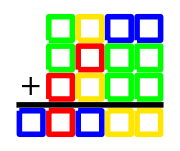

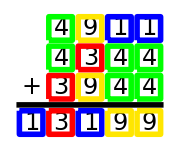

```mathematica
For[k=1,k>0,k++,digits=r[4];For[i=1,i≤3,i++,summand[i]=Table[digits⟦RandomInteger[{1,4}]⟧,{4}]];s=dtn[summand[1]]+dtn[summand[2]]+dtn[summand[3]];If[Complement[Union[IntegerDigits[s]],digits]=={},ss=Table[summand[i],{i,1,3}];s1=ss/.{digits⟦1⟧->"A",digits⟦2⟧->"B",digits⟦3⟧->"C",digits⟦4⟧->"D"};s2=IntegerDigits[s]/.{digits⟦1⟧->"A",digits⟦2⟧->"B",digits⟦3⟧->"C",digits⟦4⟧->"D"};ct=0;For[j1=1,j1≤9,j1++,For[j2=1,j2≤9,j2++,For[j3=1,j3≤9,j3++,For[j4=1,j4≤9,j4++,If[Length[Union[{j1,j2,j3,j4}]]==4&&Total[dtn/@(s1/.{"A"->j1,"B"->j2,"C"->j3,"D"->j4})]==dtn[s2/.{"A"->j1,"B"->j2,"C"->j3,"D"->j4}],ct++]]]]];If[ct==1,gr[ss,s1,IntegerDigits[s],s2];Print[]]]]
```

```mathematica
gr[L_,s1_,s_,s2_]:=Module[{},Print[Show[Graphics[{AbsoluteThickness[4],Text[Style["+",FontSize->28],{0,1}],If[Length[s]==4,Line[{{0.5,0.4},{5.5,0.4}}],Line[{{-0.5,0.4},{5.5,0.4}}]],Table[{col[s1⟦ii,jj⟧],Line[{{jj-0.4,ii-0.4},{jj+0.4,ii-0.4},{jj+0.4,ii+0.4},{jj-0.4,ii+0.4},{jj-0.4,ii-0.4}}]},{ii,1,3},{jj,1,5}],Table[{col[s2⟦ii⟧],Line[{{ii-Length[s]+5-0.4,0.2},{ii-Length[s]+5+0.4,0.2},{ii-Length[s]+5+0.4,-0.6},{ii-Length[s]+5-0.4,-0.6},{ii-Length[s]+5-0.4,0.2}}]},{ii,1,Length[s]}]}],AspectRatio->Automatic,ImageSize->200,PlotRange->{{-0.5,5.5},{-0.7,3.5}}]];Print[Show[Graphics[{AbsoluteThickness[4],Table[Text[Style[L⟦ii,jj⟧,FontSize->24,FontFamily->"Courier"],{jj+0.02,ii}],{ii,1,3},{jj,1,5}],Text[Style["+",FontSize->24,FontFamily->"Courier"],{0,1}],Table[Text[Style[s⟦ii⟧,FontSize->24,FontFamily->"Courier"],{ii-Length[s]+5+0.02,-0.2}],{ii,1,Length[s]}],If[Length[s]==4,Line[{{0.5,0.4},{5.5,0.4}}],Line[{{-0.5,0.4},{5.5,0.4}}]],Table[{col[s1⟦ii,jj⟧],Line[{{jj-0.4,ii-0.4},{jj+0.4,ii-0.4},{jj+0.4,ii+0.4},{jj-0.4,ii+0.4},{jj-0.4,ii-0.4}}]},{ii,1,3},{jj,1,5}],Table[{col[s2⟦ii⟧],Line[{{ii-Length[s]+5-0.4,0.2},{ii-Length[s]+5+0.4,0.2},{ii-Length[s]+5+0.4,-0.6},{ii-Length[s]+5-0.4,-0.6},{ii-Length[s]+5-0.4,0.2}}]},{ii,1,Length[s]}]}],AspectRatio->Automatic,ImageSize->200,PlotRange->{{-0.5,5.5},{-0.7,3.5}}]]]
```

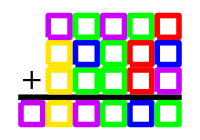

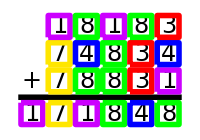

```mathematica
For[k=1,k>0,k++,digits=r[5];For[i=1,i≤3,i++,summand[i]=Table[digits⟦RandomInteger[{1,5}]⟧,{5}]];s=dtn[summand[1]]+dtn[summand[2]]+dtn[summand[3]];ss=Table[summand[i],{i,1,3}];s1=ss/.{digits⟦1⟧->"A",digits⟦2⟧->"B",digits⟦3⟧->"C",digits⟦4⟧->"D",digits⟦5⟧->"E"};s2=IntegerDigits[s]/.{digits⟦1⟧->"A",digits⟦2⟧->"B",digits⟦3⟧->"C",digits⟦4⟧->"D",digits⟦5⟧->"E"};If[Complement[Union[IntegerDigits[s]],digits]=={}&&Length[Union[Sort/@Transpose[s1]]]==5&&Min[Table[Count[Flatten[Join[ss,IntegerDigits[s]]],digits⟦g⟧],{g,1,5}]]>2,ct=0;For[j1=1,j1≤9,j1++,For[j2=1,j2≤9,j2++,For[j3=1,j3≤9,j3++,For[j4=1,j4≤9,j4++,For[j5=1,j5≤9,j5++,If[Length[Union[{j1,j2,j3,j4,j5}]]==5&&Total[dtn/@(s1/.{"A"->j1,"B"->j2,"C"->j3,"D"->j4,"E"->j5})]==dtn[s2/.{"A"->j1,"B"->j2,"C"->j3,"D"->j4,"E"->j5}],ct++]]]]]];If[ct==1,gr[ss,s1,IntegerDigits[s],s2];Print[]]]]
```

```mathematica
r[n_]:=Module[{a,b},a={};For[i=1,i≤n,i++,b=RandomInteger[{1,9}];While[MemberQ[a,b],b=RandomInteger[{1,9}]];AppendTo[a,b]];a]
```

```mathematica
dtn[L_]:=Fold[10#1+#2&,0,L]
```

```mathematica
col["A",{x_,y_}]:=Line[{{x-.4,y-.4},{x-.4,y+.4},{x+.4,y+.4},{x+.4,y-.4},{x-.4,y-.4}}]
col["B",{x_,y_}]:=Circle[{x,y},.4]
col["C",{x_,y_}]:=Line[{{x-.45,y-.4},{x+.45,y-.4},{x,y+.4},{x-.45,y-.4}}]
col["D",{x_,y_}]:=Line[Table[{x,y}+{.45Cos[2 Pi ij/5+Pi/10],.45Sin[2 Pi ij/5+Pi/10]-.02},{ij,0,5}]]
```

```mathematica
gr[L_,s1_,s_,s2_]:=Module[{},Print[Show[Graphics[{AbsoluteThickness[3],Text[Style["+",FontSize->32],{0,1}],If[Length[s]==4,Line[{{0.5,0.4},{4.5,0.4}}],Line[{{-0.5,0.4},{4.5,0.4}}]],Table[col[s1⟦ii,jj⟧,{jj,ii}],{ii,1,3},{jj,1,4}],Table[col[s2⟦ii⟧,{ii-Length[s]+4,-.2}],{ii,1,Length[s]}]}],AspectRatio->Automatic,ImageSize->200,PlotRange->{{-0.5,4.5},{-0.7,3.5}}]];Print[Show[Graphics[{AbsoluteThickness[3],Table[Text[Style[L⟦ii,jj⟧,FontSize->18,FontFamily->"Courier"],{jj+0.02,ii-.1}],{ii,1,3},{jj,1,4}],Table[Text[Style[s⟦ii⟧,FontSize->18,FontFamily->"Courier"],{ii-Length[s]+4+0.02,-0.35}],{ii,1,Length[s]}],Text[Style["+",FontSize->32],{0,1}],If[Length[s]==4,Line[{{0.5,0.4},{4.5,0.4}}],Line[{{-0.5,0.4},{4.5,0.4}}]],Table[col[s1⟦ii,jj⟧,{jj,ii}],{ii,1,3},{jj,1,4}],Table[col[s2⟦ii⟧,{ii-Length[s]+4,-.2}],{ii,1,Length[s]}]}],AspectRatio->Automatic,ImageSize->200,PlotRange->{{-0.5,4.5},{-0.7,3.5}}]]]
```

```mathematica
AQ={{1,2,3,4},{2,3,4,5},{2,3,4,6},{2,3,5,6},{2,4,5,6},{2,4,6,8}};
For[k=1,k>0,k++,digits=r[4];
For[i=1,i≤3,i++,summand[i]=Table[digits⟦RandomInteger[{1,4}]⟧,{4}]];s=dtn[summand[1]]+dtn[summand[2]]+dtn[summand[3]];
If[Complement[Union[IntegerDigits[s]],digits]=={},ss=Table[summand[i],{i,1,3}];s1=ss/.{digits⟦1⟧->"A",digits⟦2⟧->"B",digits⟦3⟧->"C",digits⟦4⟧->"D"};s2=IntegerDigits[s]/.{digits⟦1⟧->"A",digits⟦2⟧->"B",digits⟦3⟧->"C",digits⟦4⟧->"D"};If[Min[Table[Count[Flatten[{s1,s2}],{"A","B","C","D"}[[ij]]],{ij,1,4}]]>2,
ct=0;
For[j1=0,j1≤9,j1++,
For[j2=0,j2≤9,j2++,
For[j3=0,j3≤9,j3++,
For[j4=0,j4≤9,j4++,If[Length[Union[{j1,j2,j3,j4}]]==4&&Total[dtn/@(s1/.{"A"->j1,"B"->j2,"C"->j3,"D"->j4})]==dtn[s2/.{"A"->j1,"B"->j2,"C"->j3,"D"->j4}],ct++]]]]];If[ct==1,AppendTo[AQ,Sort[digits]];gr[ss,s1,IntegerDigits[s],s2];]]]]
```

## 1235

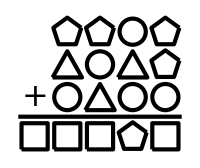

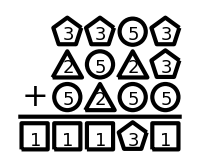

## 1236

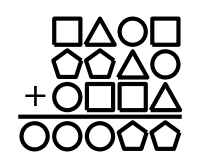

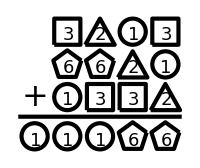

## 1237

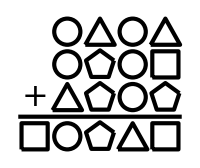

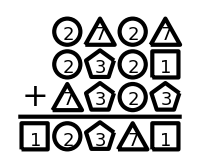

## 1238

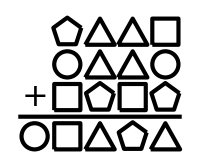

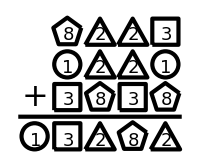

## 1239

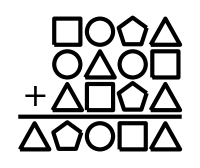

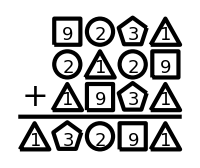

## 1245

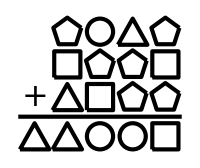

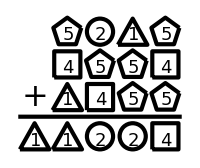

## 1246

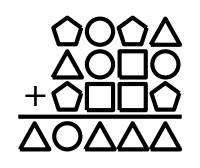

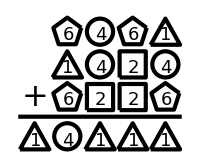

## 1247

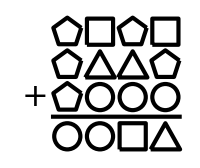

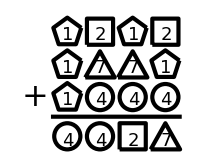

## 1248

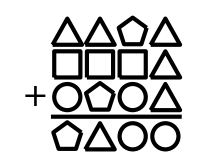

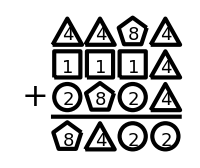

## 1249

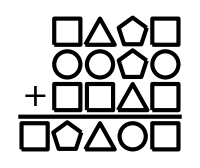

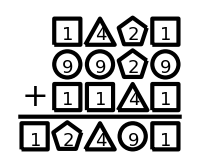

## 1256

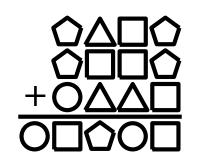

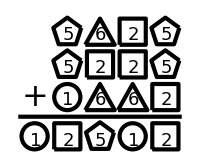

## 1257

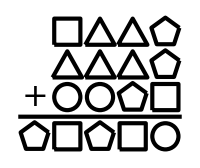

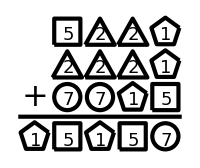

## 1258

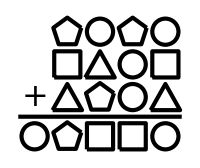

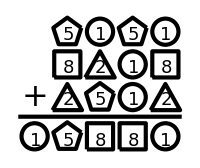

## 1259

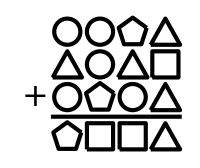

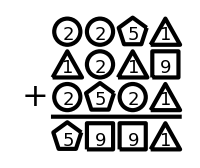

## 1267

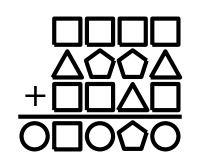

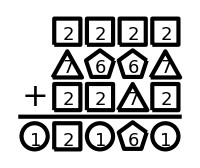

## 1268

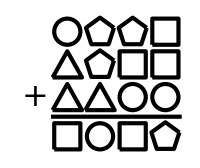

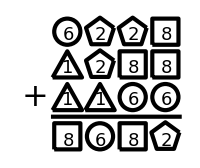

## 1269

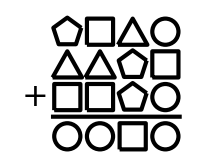

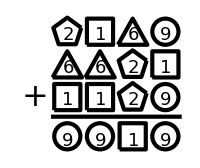

## 1278

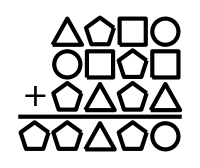

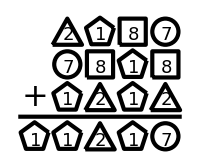

## 1279

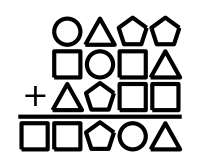

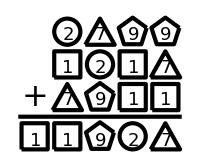

## 1289

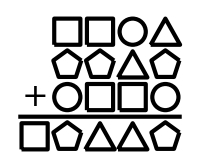

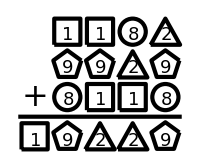

## 1345

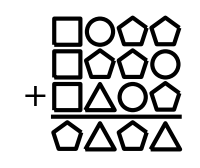

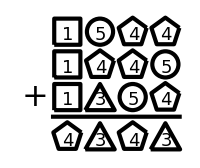

## 1346

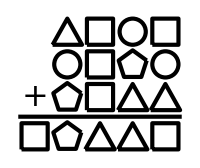

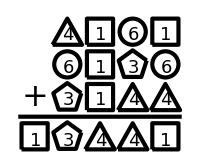

## 1347

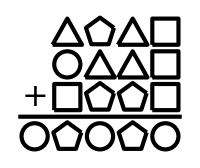

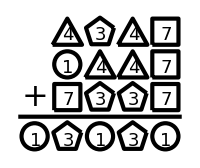

## 1348

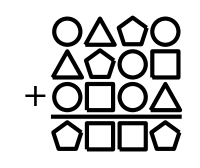

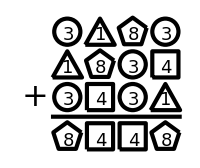

## 1349

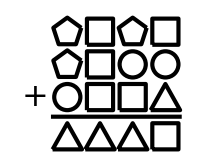

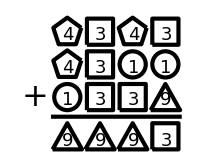

## 1356

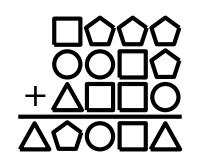

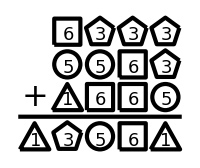

## 1357

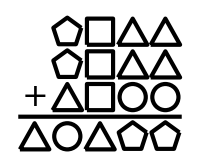

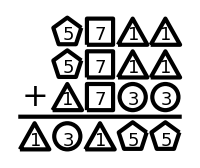

## 1358

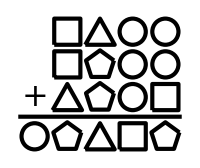

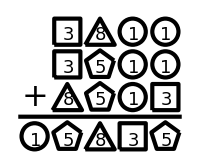

## 1359

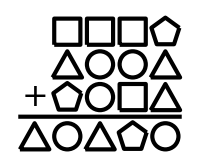

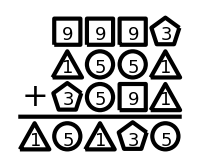

## 1367

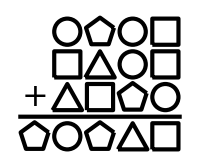

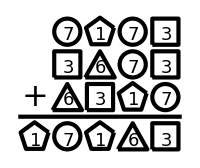

## 1368

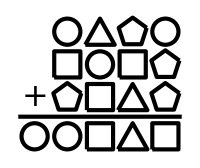

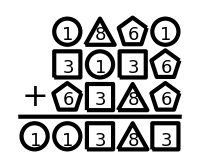

## 1369

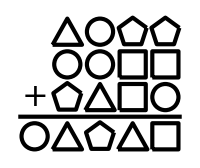

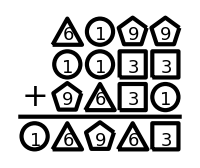

## 1378

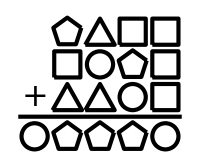

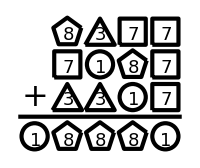

## 1379

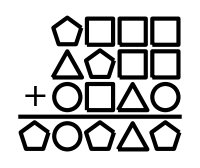

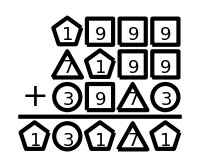

## 1389

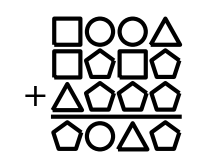

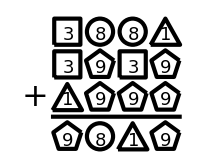

## 1456

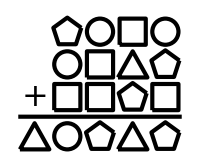

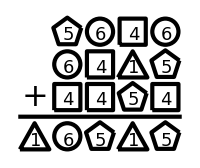

## 1457

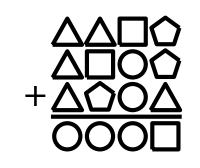

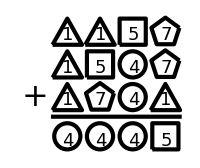

## 1458

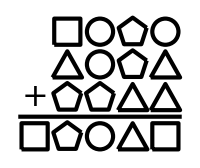

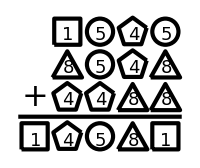

## 1459

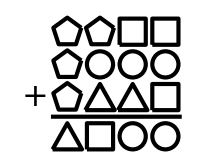

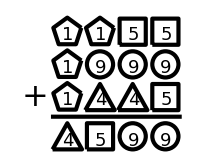

## 1467

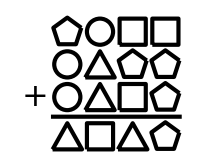

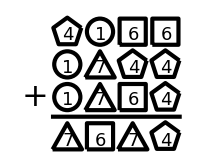

## 1468

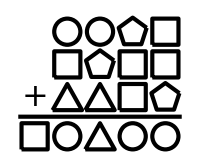

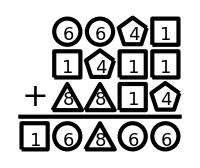

## 1469

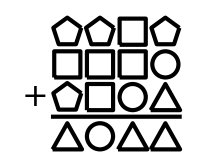

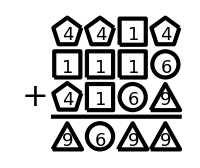

## 1478

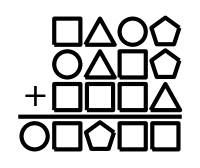

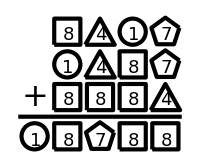

## 1479

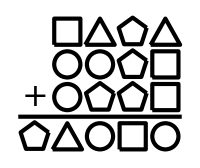

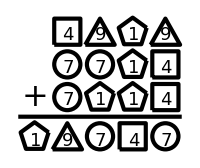

## 1489

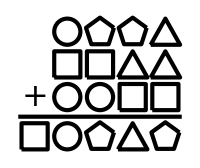

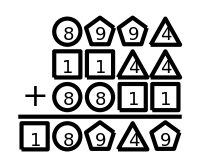

## 1567

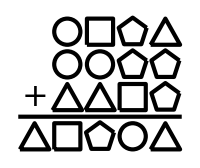

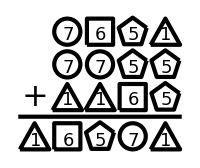

## 1568

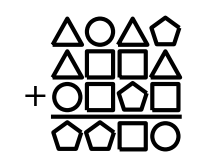

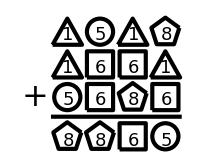

## 1569

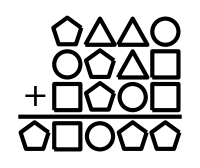

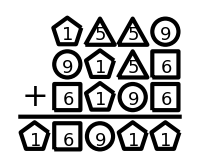

## 1578

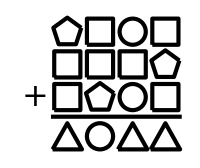

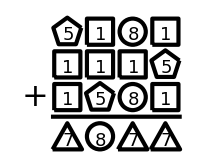

## 1579

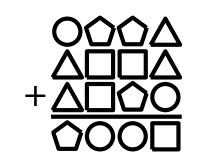

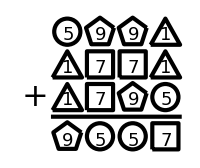

## 1589

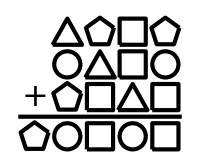

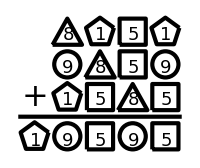

## 1678

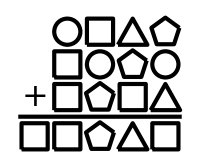

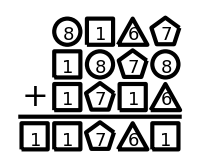

## 1679

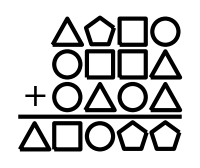

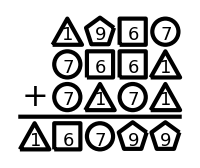

## 1689

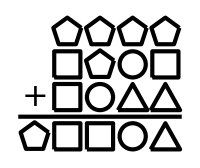

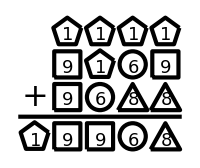

## 2347

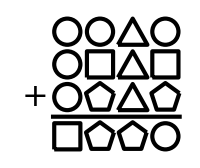

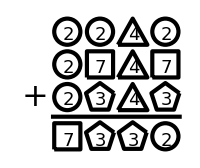

## 2348

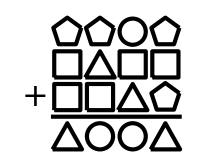

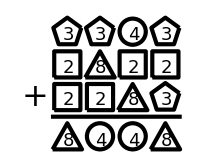

## 2349

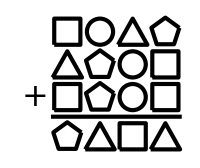

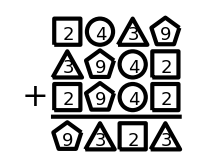

## 2357

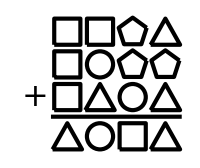

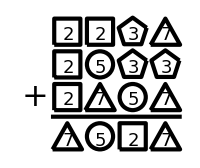

## 2358

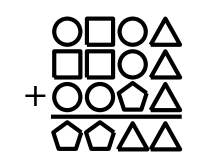

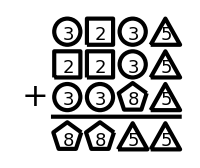

## 2359

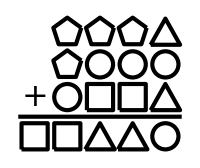

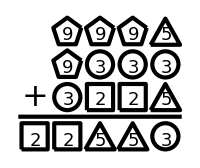

## 2367

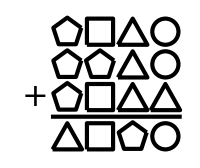

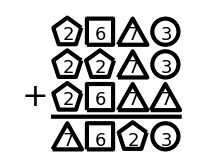

## 2368

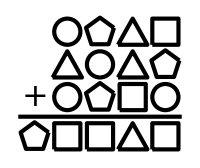

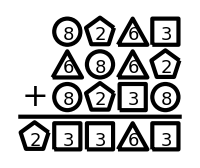

## 2369

-Graphics-

-Graphics-

## 2378

-Graphics-

-Graphics-

## 2379

-Graphics-

-Graphics-

## 2389

-Graphics-

-Graphics-

## 2457

-Graphics-

-Graphics-

## 2458

-Graphics-

-Graphics-

## 2459

-Graphics-

-Graphics-

## 2467

-Graphics-

-Graphics-

## 2469

-Graphics-

-Graphics-

## 2478

-Graphics-

-Graphics-

## 2479

-Graphics-

-Graphics-

## 2489

-Graphics-

-Graphics-

## 2567

-Graphics-

-Graphics-

## 2568

-Graphics-

-Graphics-

## 2569

-Graphics-

-Graphics-

## 2578

-Graphics-

-Graphics-

## 2579

-Graphics-

-Graphics-

## 2589

-Graphics-

-Graphics-

## 2678

-Graphics-

-Graphics-

## 2679

-Graphics-

-Graphics-

## 2689

-Graphics-

-Graphics-

## 2789

-Graphics-

-Graphics-

## 3 symbols

```mathematica
col["A",{x_,y_}]:=Line[{{x-.4,y-.4},{x-.4,y+.4},{x+.4,y+.4},{x+.4,y-.4},{x-.4,y-.4}}]
col["B",{x_,y_}]:=Circle[{x,y},.4]
col["C",{x_,y_}]:=Line[{{x-.45,y-.4},{x+.45,y-.4},{x,y+.4},{x-.45,y-.4}}]
col["D",{x_,y_}]:=Line[Table[{x,y}+{.45Cos[2 Pi ij/5+Pi/10],.45Sin[2 Pi ij/5+Pi/10]-.02},{ij,0,5}]]
```

```mathematica
gr[L_,s1_,s_,s2_]:=Module[{},Print[Show[Graphics[{AbsoluteThickness[2],Text[Style["+",FontSize->32],{0,1}],If[Length[s]==5,Line[{{0.5,0.4},{length+.5`,0.4}}],Line[{{-0.5,0.4},{length+.5`,0.4}}]],Table[col[s1⟦ii,jj⟧,{jj,ii}],{ii,1,4},{jj,1,length}],Table[col[s2⟦ii⟧,{ii-Length[s]+length,-.2}],{ii,1,Length[s]}]}],AspectRatio->Automatic,ImageSize->180,PlotRange->{{-0.5,4.5},{-0.7,4.5}}]];Print[Show[Graphics[{AbsoluteThickness[2],Table[Text[Style[L⟦ii,jj⟧,FontSize->18,FontFamily->"Courier"],{jj+0.02,ii-.1}],{ii,1,4},{jj,1,length}],Table[Text[Style[s⟦ii⟧,FontSize->18,FontFamily->"Courier"],{ii-Length[s]+length+0.02,-0.35}],{ii,1,Length[s]}],Text[Style["+",FontSize->32],{0,1}],If[Length[s]==5,Line[{{0.5,0.4},{length+.5`,0.4}}],Line[{{-0.5,0.4},{length+.5`,0.4}}]],Table[col[s1⟦ii,jj⟧,{jj,ii}],{ii,1,4},{jj,1,length}],Table[col[s2⟦ii⟧,{ii-Length[s]+length,-.2}],{ii,1,Length[s]}]}],AspectRatio->Automatic,ImageSize->180,PlotRange->{{-0.5,4.5},{-0.7,4.5}}]]]
```

```mathematica
shapes=3;length=3;
AQ={};
For[k=1,k>0,k++,digits=r[shapes];
While[MemberQ[AQ,Sort[digits]],digits=r[shapes]];
For[i=1,i≤4,i++,summand[i]=Table[digits⟦RandomInteger[{1,shapes}]⟧,{length}]];s=dtn[summand[1]]+dtn[summand[2]]+dtn[summand[3]]+dtn[summand[4]];
If[s<1000,
If[Complement[Union[IntegerDigits[s]],digits]=={},ss=Table[summand[i],{i,1,4}];s1=ss/.{digits⟦1⟧->"A",digits⟦2⟧->"B",digits⟦3⟧->"C"};s2=IntegerDigits[s]/.{digits⟦1⟧->"A",digits⟦2⟧->"B",digits⟦3⟧->"C"};If[Min[Table[Count[Flatten[{s1,s2}],{"A","B","C"}[[ij]]],{ij,1,shapes}]]>2,
ct=0;
For[j1=1,j1≤9,j1++,
For[j2=1,j2≤9,j2++,
For[j3=1,j3≤9,j3++,
If[Length[Union[{j1,j2,j3}]]==3&&Total[dtn/@(s1/.{"A"->j1,"B"->j2,"C"->j3})]==dtn[s2/.{"A"->j1,"B"->j2,"C"->j3}],ct++]]]]];If[ct==1,AppendTo[AQ,Sort[digits]];Print[Style[Sort[digits],FontSize->30]];gr[ss,s1,IntegerDigits[s],s2];]]]]
```

{1,2,7}

-Graphics-

-Graphics-

{1,2,9}

-Graphics-

-Graphics-

{1,2,6}

-Graphics-

-Graphics-

{1,4,8}

-Graphics-

-Graphics-

{1,2,8}

-Graphics-

-Graphics-

{1,3,8}

-Graphics-

-Graphics-

{2,7,9}

-Graphics-

-Graphics-

{1,5,6}

-Graphics-

-Graphics-

{1,4,5}

-Graphics-

-Graphics-

{2,5,9}

-Graphics-

-Graphics-

{1,6,9}

-Graphics-

-Graphics-

{1,4,6}

-Graphics-

-Graphics-

{1,6,7}

-Graphics-

-Graphics-

{2,3,9}

-Graphics-

-Graphics-

{1,6,8}

-Graphics-

-Graphics-

{1,4,9}

-Graphics-

-Graphics-

{2,4,9}

-Graphics-

-Graphics-

{1,7,8}

-Graphics-

-Graphics-

{1,5,8}

-Graphics-

-Graphics-

{2,6,9}

-Graphics-

-Graphics-

{1,2,5}

-Graphics-

-Graphics-

{1,4,7}

-Graphics-

-Graphics-

{1,3,6}

-Graphics-

-Graphics-

$Aborted